# Model 1: Plotting

This file contains the processing code for Model 1: Effects of Autocorrelation Across the Thermal Landscape. Before running this file, you must have extinction time outputs from running Model 1 on a TPC using Model1.nb; edit import and export locations (via ‘saveto’) for your own device.

## Load Data

Run import code before creating any figures. Edit the import/export file names/locations for your local system and, if necessary, edit loaded parameter space to match your imported run. Default size is tmax2000_dims21,7,7,1000, corresponding with 1000 runs of 2000 time steps at each of 21 autocorrelation levels, 7 mean temperatures, and 7 standard deviations of temperature. Choose outputs for either the temperate or the tropical TPC. Subfigures from this file were combined using Adobe Illustrator 2024.

```mathematica
saveto="/Users/alisonrobey/Desktop/"; (*edit import/export location here*)
extTime=Import[saveto<>"/extTime_trop_tmax2000_dims21,7,7,1000.m","MX"]; (*edit import location here; use extTime_tmax for temperature and extTime_trop_tmax for tropical*)

γvals=Range[0,2,.1]; (*21*)
μTvals=Range[23,26,.5];  (*7*)
σTvals=Range[1,4,.5];  (*7*)
```

## Figure 3a: Proportion Extinct

Calculate the proportion of simulations to go extinct at each point in the parameter space, then plot the corresponding heat maps of extinction risk for each parameter combination. Results not shown in main paper are included in Appendix S5.

```mathematica
propExt=ConstantArray[0,{21,7,7}];
Do[propExt[[i,j,k]]=Count[extTime[[i,j,k]],2000]/1000,{i,1,21},{j,1,7},{k,1,7}]
```

Subplot of autocorrelation against mean temperature at each value of the standard deviation.

```mathematica
propExt1=Reverse[propExt[[All,All,1]]];
propExt2=Reverse[propExt[[All,All,2]]];
propExt3=Reverse[propExt[[All,All,3]]];
propExt4=Reverse[propExt[[All,All,4]]];
propExt5=Reverse[propExt[[All,All,5]]];
propExt6=Reverse[propExt[[All,All,6]]];
propExt7=Reverse[propExt[[All,All,7]]];

plotRange={Min[propExt7],Max[propExt1]}; (*standardize color scale*)
imagesize=80; (*80 for exporting in one row, 100 for higher visibility in Mathematica*)

newmap[x_]:=Blend[{RGBColor["#ffffd9"],RGBColor["#edf8b1"],RGBColor["#c7e9b4"],RGBColor["#7fcdbb"],RGBColor["#41b6c4"],RGBColor["#4eb3d3"],RGBColor["#2b8cbe"],RGBColor["#0868ac"],RGBColor["#084081"]},1-x];

propExtAutoMeansPlot=
Labeled[
Row[{ArrayPlot[propExt1,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=1",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[propExt2,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=1.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[propExt3,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=2",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[propExt4,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=2.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[propExt5,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=3",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[propExt6,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=3.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[propExt7,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=4",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}},PlotLegends->Placed[BarLegend[{newmap,plotRange},LegendLabel->Placed[Rotate[Style["Proportion Persisting",15],90 Degree],Left]],Right]]
}],{"Mean Temperature",Rotate["Autocorrelation Level",90 Degree]},{Bottom,Left}]

Export[saveto<>"extTime3_2000_AutoMeansPropsPlot.pdf",propExtAutoMeansPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Mean TemperatureAutocorrelation Level

Subplot of autocorrelation against standard deviation of temperature at each mean temperature.

```mathematica
propExt1=Reverse[propExt[[All,1,All]]];
propExt2=Reverse[propExt[[All,2,All]]];
propExt3=Reverse[propExt[[All,3,All]]];
propExt4=Reverse[propExt[[All,4,All]]];
propExt5=Reverse[propExt[[All,5,All]]];
propExt6=Reverse[propExt[[All,6,All]]];
propExt7=Reverse[propExt[[All,7,All]]];

plotRange={Min[propExt7],Max[propExt1]};
imagesize=80;

propExtAutoStdsPlot=
Labeled[
Row[{ArrayPlot[propExt1,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=23",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[propExt2,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=23.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt3,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=24",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[propExt4,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=24.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt5,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=25",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[propExt6,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=25.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt7,ColorFunction->(newmap),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"μT=26",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}},PlotLegends->Placed[BarLegend[{newmap,plotRange},LegendLabel->Placed[Rotate[Style["Proportion Persisting",15],90 Degree],Left]],Right]]}],{"Standard Deviation of Temperature",Rotate["Autocorrelation Level",90 Degree]},{Bottom,Left}]

Export[saveto<>"extTime3_2000_AutoStdevsPropsPlot.pdf",propExtAutoStdsPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Standard Deviation of TemperatureAutocorrelation Level

Subplot of mean temperature against standard deviation of temperature at 5 of the 21 autocorrelation levels.

```mathematica
propExt1=Reverse[propExt[[1,All,All]]];
propExt2=Reverse[propExt[[6,All,All]]];
propExt3=Reverse[propExt[[11,All,All]]];
propExt4=Reverse[propExt[[16,All,All]]];
propExt5=Reverse[propExt[[21,All,All]]];

plotRange={Min[propExt5],Max[propExt1]};
imagesize=120; (*120 for exporting in one row, 180 for visibility in Mathematica*)

propExtMeansStdsPlot=Labeled[
Row[{ArrayPlot[propExt1,ColorFunction->(newmap),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=0",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt2,ColorFunction->(newmap),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=.5",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[propExt3,ColorFunction->(newmap),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=1",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt4,ColorFunction->(newmap),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=1.5",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[propExt5,ColorFunction->(newmap),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=2",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}},PlotLegends->Placed[BarLegend[{newmap,plotRange},LegendLabel->Placed[Rotate[Style["Proportion Persisting",15],90 Degree],Left]],Right]]}],{"Standard Deviation of Temperature",Rotate["Mean Temperature",90 Degree]},{Bottom,Left}]

Export[saveto<>"extTime3_2000_MeansStdsPropsPlot.pdf",propExtMeansStdsPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics-Standard Deviation of TemperatureMean Temperature

## Figure 3b: Time to Extinction

Calculate the average time to extinction across simulations at each point in the parameter space, then plot the corresponding heat maps of extinction time for each parameter combination. Results not shown in main paper are included in Appendix S5.

```mathematica
extTimeMeans=ConstantArray[0,{21,7,7}];
Do[extTimeMeans[[i,j,k]]=Mean[extTime[[i,j,k]]],{i,1,21},{j,1,7},{k,1,7}]

extTimeStds=ConstantArray[0,{21,7,7}];
Do[extTimeStds[[i,j,k]]=StandardDeviation[extTime[[i,j,k]]],{i,1,21},{j,1,7},{k,1,7}]
```

Subplot of autocorrelation against mean temperature at each value of the standard deviation.

```mathematica
heatmapdata1=Reverse[extTimeMeans[[All,All,1]]];
heatmapdata2=Reverse[extTimeMeans[[All,All,2]]];
heatmapdata3=Reverse[extTimeMeans[[All,All,3]]];
heatmapdata4=Reverse[extTimeMeans[[All,All,4]]];
heatmapdata5=Reverse[extTimeMeans[[All,All,5]]];
heatmapdata6=Reverse[extTimeMeans[[All,All,6]]];
heatmapdata7=Reverse[extTimeMeans[[All,All,7]]];

plotRange={Min[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5,heatmapdata6,heatmapdata7],Max[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5,heatmapdata6,heatmapdata7]};
imagesize=80;

extTimeAutoMeansPlot=Labeled[
Row[{ArrayPlot[heatmapdata1,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=1",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[heatmapdata2,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=1.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[heatmapdata3,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=2",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[heatmapdata4,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=2.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[heatmapdata5,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=3",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],ArrayPlot[heatmapdata6,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=3.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}}],
ArrayPlot[heatmapdata7,ColorFunction->(ColorData["TemperatureMap"][1-#]&),PlotRange->plotRange,ImageSize->imagesize,PlotLabel->"σT=4",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,23},{4,24.5},{7,26}},None}},PlotLegends->Placed[BarLegend[{ColorData["TemperatureMap"][1-#]&,plotRange},LegendLabel->"extTime"],Right]]
}],{"Mean Temperature",Rotate["Autocorrelation Level",90 Degree]},{Bottom,Left}]

Export[saveto<>"extTime3_2000_AutoMeansPlot.pdf",extTimeAutoMeansPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Mean TemperatureAutocorrelation Level

Subplot of autocorrelation against standard deviation of temperature at each mean temperature.

```mathematica
heatmapdata1=Reverse[extTimeMeans[[All,1,All]]];
heatmapdata2=Reverse[extTimeMeans[[All,2,All]]];
heatmapdata3=Reverse[extTimeMeans[[All,3,All]]];
heatmapdata4=Reverse[extTimeMeans[[All,4,All]]];
heatmapdata5=Reverse[extTimeMeans[[All,5,All]]];
heatmapdata6=Reverse[extTimeMeans[[All,6,All]]];
heatmapdata7=Reverse[extTimeMeans[[All,7,All]]];

plotRange={Min[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5,heatmapdata6,heatmapdata7],Max[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5,heatmapdata6,heatmapdata7]};
imagesize=80;

extTimeAutoStdsPlot=Labeled[
Row[{ArrayPlot[heatmapdata1,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=23",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[heatmapdata2,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=23.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata3,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=24",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[heatmapdata4,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=24.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata5,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=25",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[heatmapdata6,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=25.5",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata7,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->imagesize,PlotRange->plotRange,PlotLabel->"μT=26",FrameTicks->{{{{1,2},{11,1},{21,0}},None},{{{1,1},{4,2.5},{7,4}},None}},PlotLegends->Placed[BarLegend[{ColorData["TemperatureMap"][1-#]&,plotRange},LegendLabel->"extTime"],Right]]
}],{"Standard Deviation of Temperature",Rotate["Autocorrelation Level",90 Degree]},{Bottom,Left}
]

Export[saveto<>"extTime3_2000_AutoStdsPlot.pdf",extTimeAutoStdsPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics--Graphics--Graphics-Standard Deviation of TemperatureAutocorrelation Level

Subplot of mean temperature against standard deviation of temperature at 5 of the 21 autocorrelation levels.

```mathematica
heatmapdata1=Reverse[extTimeMeans[[1,All,All]]];
heatmapdata2=Reverse[extTimeMeans[[6,All,All]]];
heatmapdata3=Reverse[extTimeMeans[[11,All,All]]];
heatmapdata4=Reverse[extTimeMeans[[16,All,All]]];
heatmapdata5=Reverse[extTimeMeans[[21,All,All]]];

plotRange={Min[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5],Max[heatmapdata1,heatmapdata2,heatmapdata3,heatmapdata4,heatmapdata5]};
imagesize=120; (*120 for exporting in one row, 180 for visibility in mathematica*)

extTimeMeansStdsPlot=Labeled[
Row[{ArrayPlot[heatmapdata1,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=0",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata2,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=.5",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],ArrayPlot[heatmapdata3,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=1",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata4,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=1.5",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}}],
ArrayPlot[heatmapdata5,ColorFunction->(ColorData["TemperatureMap"][1-#]&),ImageSize->120,PlotRange->plotRange,PlotLabel->"γ=2",FrameTicks->{{{{1,26},{4,24.5},{7,23}},None},{{{1,1},{4,2.5},{7,4}},None}},PlotLegends->Placed[BarLegend[{ColorData["TemperatureMap"][1-#]&,plotRange},LegendLabel->"extTime"],Right]]
}],{"Standard Deviation of Temperature",Rotate["Mean Temperature",90 Degree]},{Bottom,Left}]

Export[saveto<>"extTime3_2000_MeansStdsPlot.pdf",extTimeMeansStdsPlot,ImageResolution->1000];
```

-Graphics--Graphics--Graphics--Graphics--Graphics-Standard Deviation of TemperatureMean Temperature

Create histograms of extinction time for some sample parameter sets.

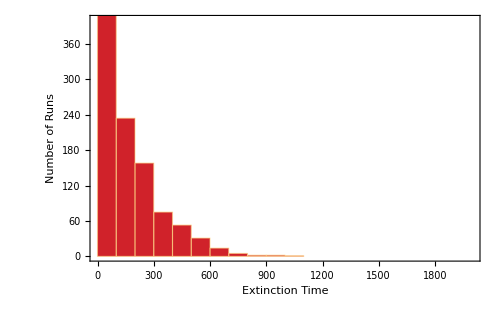

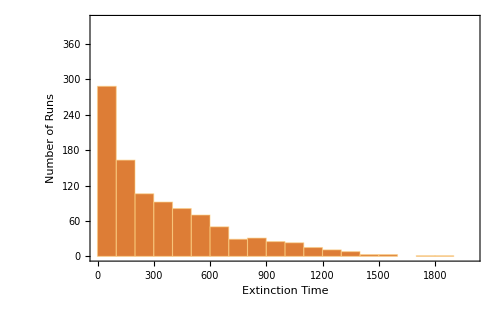

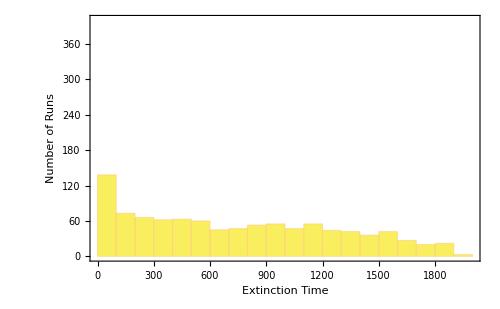

```mathematica
data1=extTime[[1,7,7]]; (*white noise*)
data2=extTime[[11,7,7]]; (*pink noise*)
data3=extTime[[21,7,7]]; (*brown noise*)

hist1=Histogram[data1,10,ChartStyle->{ColorData["TemperatureMap",1]},(*ChartLabels->{"γ=0"},*)PlotRange->{{0,2000},{0,400}}, Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Extinction Time","Number of Runs"},LabelStyle->Directive[Black],ImageSize->500]
hist2=Histogram[data2,20,ChartStyle->{ColorData["TemperatureMap",.9]},(*ChartLabels->{"γ=1"},*)PlotRange->{{0,2000},{0,400}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Extinction Time","Number of Runs"},LabelStyle->Directive[Black],ImageSize->500]
hist3=Histogram[data3,20,ChartStyle->{ColorData["TemperatureMap",.7]},(*ChartLabels->{"γ=2"},*)PlotRange->{{0,2000},{0,400}},Frame->{True,True,False,False},FrameStyle->14,FrameLabel->{"Extinction Time","Number of Runs"},LabelStyle->Directive[Black],ImageSize->500]

Export[saveto<>"extTime3_trop_hist1,7,7.pdf",hist1,ImageResolution->1000];
Export[saveto<>"extTime3_trop_hist11,7,7.pdf",hist2,ImageResolution->1000];
Export[saveto<>"extTime3_trop_hist21,7,7.pdf",hist3,ImageResolution->1000];
```